# A Note on Hyperspherical Pseudorandom Vectors

Technical Report, Amazon Robotics

Brian Beckman

Principal Engineer
March, 2019

Abstract

We need spherically symmetric and spherically uniform pseudorandom vectors in d≥3 dimensions for simulation, estimation, control, machine learning, optimization, search, test generation, and more. The number of dimensions can be in the hundreds or thousands, corresponding to the number of degrees of freedom in a simulated physical system or the number of weights in a neural network. Methods like rejection sampling are not feasible in even moderate numbers of dimensions. For example, in twenty-seven dimensions, only one in a trillion points is in the d-ball and not in the d-cube.

We demonstrate two computational methods that scale efficiently to hundreds of dimensions for generating pseudorandom vectors uniformly distributed on the unit d-sphere (a hyperspherical surface) and in the unit d-ball (the interior of a hypersphere). Though neither method is novel, it is not obvious how they work. The contributions of this note are proofs, executable specifications of algorithms, and numerical demonstrations of the algorithms.

## DEFINITIONS

The unit d-ball is the interior of a hypersphere: the set of all real d-vectors (x_1,x_2,…,x_d) such that x_1^2+x_2^2+⋯+x_d^2<1. The unit d-sphere is the boundary of the d-ball, that is, the set of all real d-vectors such that x_1^2+x_2^2+⋯+x_d^2=1.

The unit d-cube is the set of all real d-vectors such that each coordinate is independently bounded in absolute value by unity, inclusively, that is, where -1≤x_(i∈[1..d])≤1. The unit d-ball, d-sphere, and d-cube are also said to have radius 1, diameter 2.

We do not distinguish between the mathematical procedure of sampling a distribution and the computational procedure of generating pseudorandoms according to a distribution. Likewise, we do not distinguish between mathematical true randoms and computational pseudorandoms.

Generating randoms uniformly means the same as generating uniform randoms. Generating randoms symmetrically means the same as generating symmetric randoms.

## UNIFORM RANDOMS IN THE D-CUBE

Given an efficient method for generating uniform random scalars in the real interval [-1..1] — in the 1-cube — it is easy and efficient to generate rectangularly symmetric, uniform randoms in the d-cube: generate randoms for each of the d coordinates independently.

Can we generate spherically symmetric uniform randoms starting with rectangularly symmetric, uniform randoms? Yes, but it takes some care to do it efficiently. The inefficiency of rejection methods is crippling: only one in a trillion points is in the 27-ball and not in the 27-cube, and the ratio gets worse exponentially as the number of dimensions increases.

Consider points uniformly distributed in the unit 2-cube, i.e., the unit square. The resulting (x,y) pairs are not uniform with angle, therefore not spherically symmetric. The following diagram illustrates:

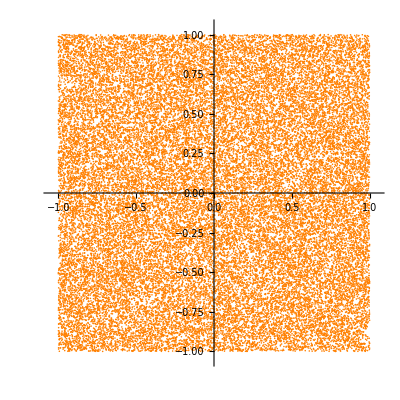

```mathematica
show2D$[points_,γ_:1.05]:=
ListPlot[Style[points,Orange],
PlotRange->{{-γ,γ},{-γ,γ}},
AspectRatio->1];
show3D$[points_,γ_:1.05]:=
ListPointPlot3D[Style[points,Orange],
PlotRange->{{-γ,γ},{-γ,γ},{-γ,γ}},
BoxRatios->{1,1,1}];
twoCubeRandoms$=
RandomVariate[
UniformDistribution[{{-1,1},{-1,1}}],
40000];
show2D$[twoCubeRandoms$]
```

There are too many points in the corners, at ArcTan[1,1]=0.7854, ArcTan[-1,1]=2.3562 and their negatives:

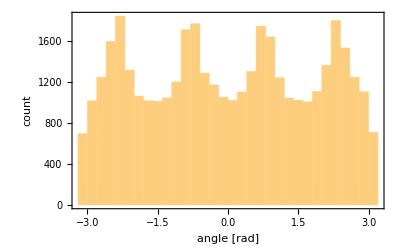

```mathematica
Histogram[MapThread[ArcTan,
{First/@twoCubeRandoms$,
First/@Rest/@twoCubeRandoms$}],
Frame->True,FrameLabel->{{"count",""},{"angle [rad]","Angle Distribution of \n40,000 Uniformly Random 2-Vectors"}}]
```

### REJECTION METHOD: IMPRACTICAL

We could reject, i.e., remove points that are not in the unit d-ball from a sample of the unit d-cube. Those would be points with radial component — Euclidean norm — greater than 1. However, the rejection strategy does not scale with dimension. As the dimension d grows, almost all the points are outside the unit d-ball, i.e., in the corners. Furthermore, the number of corners goes up as 2^d, exponentially with the number of dimensions. To show this, we compute the ratio of the volume of a unit d-ball to the volume of a unit d-cube.

What is the volume of a unit d-cube? Answer: 2^d. What is the volume of a unit d-ball?

Answer: without gamma:

```mathematica
ClearAll[vBall];
vBall[d_,r_:1]:=Piecewise[{{With[{k=d/2},π^k/(k!)r^d], Mod[d,2]===0}, {With[{k=(d-1)/2},(2k!(4π)^k)/(d!)r^d], Mod[d,2]===1}}];
Table[<|"dimension"->d,"ball volume"->vBall[d], "cube volume"->2^d,"cube/ball ratio"->N[2^d/vBall[d]]|>,{d,1,10}]//MatrixForm
```

(<|dimension→1,ball volume→2,cube volume→2,cube/ball ratio→1.|>
<|dimension→2,ball volume→π,cube volume→4,cube/ball ratio→1.27324|>
<|dimension→3,ball volume→(4 π)/3,cube volume→8,cube/ball ratio→1.90986|>
<|dimension→4,ball volume→π^2/2,cube volume→16,cube/ball ratio→3.24228|>
<|dimension→5,ball volume→(8 π^2)/15,cube volume→32,cube/ball ratio→6.07927|>
<|dimension→6,ball volume→π^3/6,cube volume→64,cube/ball ratio→12.3846|>
<|dimension→7,ball volume→(16 π^3)/105,cube volume→128,cube/ball ratio→27.0913|>
<|dimension→8,ball volume→π^4/24,cube volume→256,cube/ball ratio→63.0742|>
<|dimension→9,ball volume→(32 π^4)/945,cube volume→512,cube/ball ratio→155.222|>
<|dimension→10,ball volume→π^5/120,cube volume→1024,cube/ball ratio→401.543|>)

With gamma, arbitrary real dimensions:

```mathematica
ClearAll[vBall];
vBall[d_,r_:1]:=(π^(d/2)r^d)/Gamma[1+d/2];
```

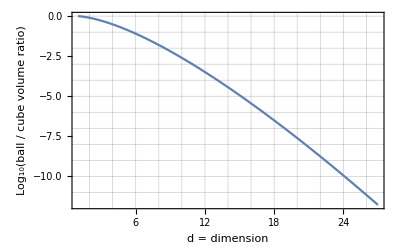

```mathematica
Plot[Log10[vBall[d]/2^d],{d,1,27},
Frame->True,GridLines->All, FrameLabel->{{"Log_10(ball / cube volume ratio)",""},{"d = dimension","Volume Ratio of Unit d-ball to Unit d-cube"}}]
```

The ratio of ball-to-cube volume in 27 dimensions is one trillionth, so the rejection method generates a trillion times more points than it keeps, is impractical.

## RADIAL SYMMETRY

Observe that a multivariate Gaussian or multinormal distribution is radially symmetric. Sampling x from (ⅇ^(-x^2/2))/(√(2 π)), and y similarly, then noticing that x and y are independent (the probability of their occurring simultaneously is the product of their individual probabilities), we get (ⅇ^(-x^2/2))/(√(2 π))×(ⅇ^(-y^2/2))/(√(2 π))=(ⅇ^(-1/2 (x^2+y^2)))/(2 π). A similar construction extends to any number of dimensions.

The multinormal distribution is radially symmetric because it depends only on the radius squared, x^2+y^2. But it is not radially uniform, as the following figure demonstrates:

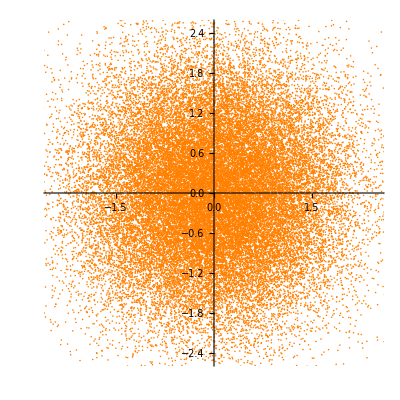

```mathematica
show2D$[RandomVariate[
MultinormalDistribution[IdentityMatrix[2]],40000],2.5]
```

## RADIAL UNIFORMITY

Due to radial symmetry, normalizing d-vectors from the d-ball produces d-vectors uniform on the d-sphere, not in the d-ball. For example, the following points are uniformly distributed on the 2-sphere:

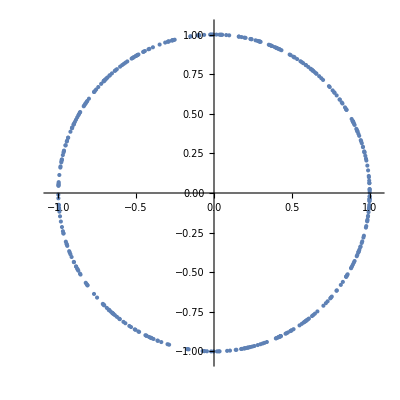

```mathematica
With[{γ=1.05},
ListPlot[Normalize/@
RandomVariate[
MultinormalDistribution[IdentityMatrix[2]],400],
PlotRange->{{-γ,γ},{-γ,γ}},AspectRatio->1]]
```

## FROM SYMMETRY TO UNIFORMITY

Now that we can generate uniform randoms on the d-sphere, the boundary of the d-ball, can we fill the interior uniformly? We show here two ways: a geometrical construction and a statistical construction.

### GEOMETRICAL CONSTRUCTION

Reduce the lengths of vectors radially, pulling their end-points toward the center, preserving radial symmetry. But how to achieve spherical uniformity? Shrinking vectors by a uniform random factor in [0,1] will not work. The results will be too sparse in outer zones and too dense in inner zones:

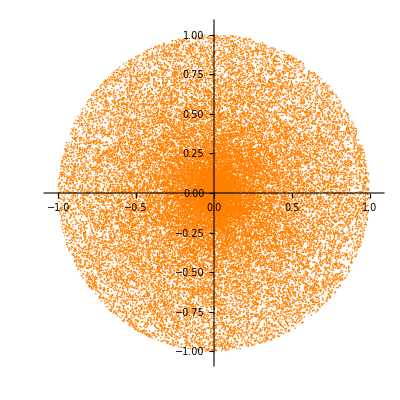

```mathematica
show2D$@With[{pointsOnSphere=
Normalize/@
RandomVariate[
MultinormalDistribution[IdentityMatrix[2]],40000],
scalar=
RandomVariate[UniformDistribution[{0,1}],40000]},
MapThread[Times,{pointsOnSphere,scalar}]]
```

If points were uniformly distributed with respect to radius r, the volume density would be proportional to r^-d=1/r^d, approaching infinity as r→0. If points were uniformly distributed in r^(1/d), then the volume density would be constant: that is what we want.

```mathematica
ClearAll[sampleDBall];
sampleDBall[d_,n_]:=
With[{
pointsOnSphere=
Normalize/@
RandomVariate[
MultinormalDistribution[IdentityMatrix[d]],n],
scalar=
Power[
RandomVariate[UniformDistribution[],n],
1/d]},
MapThread[Times,{pointsOnSphere,scalar}]];
```

The following plots illustrate points uniformly distributed in radius in two and three dimensions, and thus uniformly spherically distributed in the 2-ball and in the 3-ball, respectively:

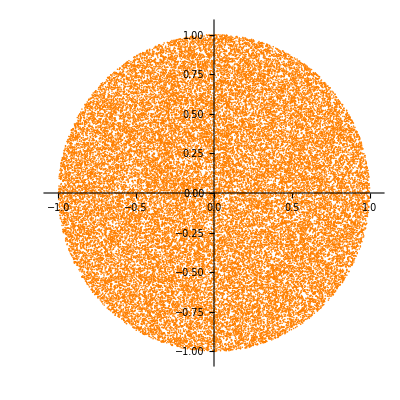

```mathematica
show2D$[sampleDBall[2,40000]]
```

```mathematica
show3D$[sampleDBall[3,40000]]
```

-Graphics3D-

### UNIFORMITY STATISTICS

We exhibit two ways to collect statistics on a sample: by shell and by cubie. From the statistics, we can calculate average point density (per unit d-volume) and check that it is uniform. The shell method counts points that lie within d-shells of constant volume. The cubie method counts points in elementary (small) d-cubes of constant volume. The shell method is robust and practical. The cubie method is obvious but naive and inaccurate or impractical for dimensions more than three. The rest of this section demonstrates.

#### BY SHELL

Consider a sequence of radii enclosing shells of equal volumes. First, divide the unit interval into increments of size dr. Radii of size d r^d enclose shells of equal volume. Shell number Ceiling[ρ^d,dr] contains the point p with Euclidean norm ρ.

The Chi-squared test for the uniform distribution demands that the standard deviation of counts in each bin be approximately equal to the square root of the mean of the counts. That observation gives us a pragmatic, “eyeball” test for uniformity.

The following are numerical statistics across 100 shells of equal volume for one million spherically uniform randoms in each of two, three, six, sixteen, and 276 dimensions. The expected mean number of points in each shell is 10,000 and the expected standard deviations of the counts is √10000=100. The empirical standard deviations agree well with the expected. A formal Chi-squared test would give us the probability that each shell is not drawn from a uniform distribution, but the agreement between empirical and expected standard deviations is good enough that a formal test does not seem necessary.

```mathematica
ClearAll[pairwise];
pairwise[fn_,list_List]:=
MapThread[fn,{Drop[list,-1],Rest[list]}];

ClearAll[pointsInShell2];
pointsInShell2[points_,d_,dr_]:=
GroupBy[points,p↦Ceiling[Norm[p]^d,dr]];

ClearAll[sampledShellCounts2];
sampledShellCounts2[deltaR_:0.01,d_:2,n_:4000,sampler_:sampleDBall]:=
With[{points=sampler[d,n]},
With[{countsAssoc=Length/@pointsInShell2[points,d,deltaR]},
Values[countsAssoc]]];

ClearAll[countsStats];
countsStats[counts_]:=
With[{𝒟=counts},
With[{
tot=Plus@@𝒟,
μ=Mean@𝒟,
σ=N@StandardDeviation@𝒟,
min=Min[𝒟],
max=Max[𝒟],
P=Quiet@FindDistribution[𝒟]},
{ListLinePlot[𝒟,PlotRange->Full],
Show[
Histogram[𝒟,Automatic,"PDF",PlotRange->Full],
Plot[PDF[P,c],{c,min,max}]],
<|"μ"->N@μ,"√μ"->N@Sqrt[μ],"σ"->σ,"tot"->tot,"min"->min,"max"->max|>}]];
```

##### TWO DIMENSIONS

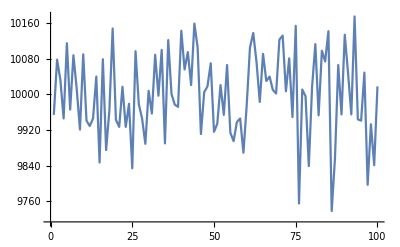
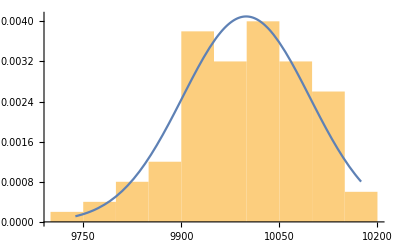
{-Graphics-,-Graphics-,<|μ→10000.,√μ→100.,σ→93.5967,tot→1000000,min→9738,max→10175|>}

```mathematica
countsStats[sampledShellCounts2[0.01,2,1000000]]
```

##### THREE DIMENSIONS

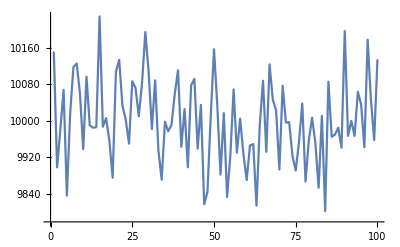
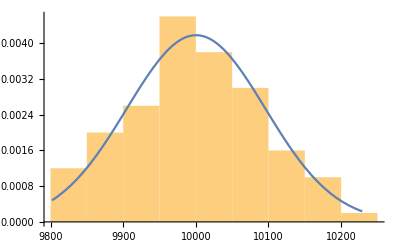
{-Graphics-,-Graphics-,<|μ→10000.,√μ→100.,σ→91.9884,tot→1000000,min→9802,max→10229|>}

```mathematica
countsStats[sampledShellCounts2[0.01,3,1000000]]
```

##### SIX DIMENSIONS

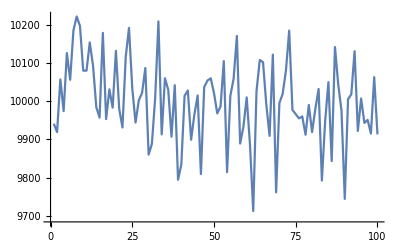
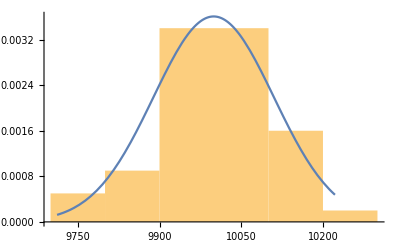
{-Graphics-,-Graphics-,<|μ→10000.,√μ→100.,σ→106.182,tot→1000000,min→9712,max→10222|>}

```mathematica
countsStats[sampledShellCounts2[0.01,6,1000000]]
```

##### SIXTEEN DIMENSIONS

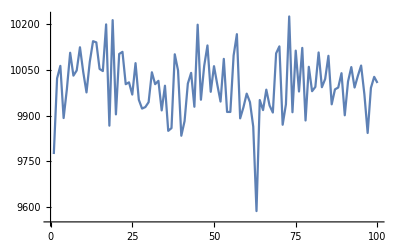
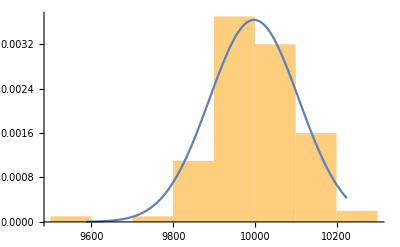
{-Graphics-,-Graphics-,<|μ→10000.,√μ→100.,σ→100.764,tot→1000000,min→9587,max→10225|>}

```mathematica
countsStats[sampledShellCounts2[0.01,16,1000000]]
```

##### 276 DIMENSIONS

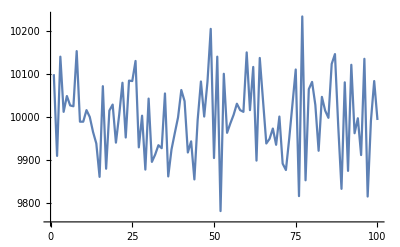
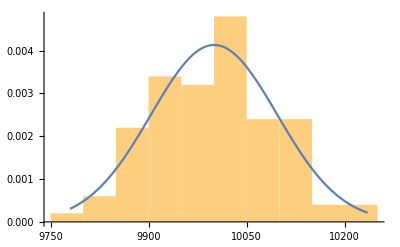
{-Graphics-,-Graphics-,<|μ→10000.,√μ→100.,σ→92.4269,tot→1000000,min→9780,max→10235|>}

```mathematica
countsStats[sampledShellCounts2[0.01,276,1000000]]
```

#### BY CUBIE

Statistics by cubie ignore geometry and count points in an evenly-spaced Cartesian grid of cubies. Statistics by shell are much faster and more informative because they honor geometry. Statistics by cubie do not scale to large dimensionalities, where almost all the volume is in the outermost cubies. Statistically, all the cubies in the outer shells will be empty. However, statistics by cubie are interesting in small dimensionalities. The code is instructive, illustrating indexing by hashing cubie coordinates.

```mathematica
ClearAll[quantum];
quantum[x_,δ_]:=
{Floor[x,δ],Ceiling[x,δ]};

ClearAll[makeCubifer];
makeCubifer[δ_]:=
Function[{dict,point},
Module[{temp=dict},
With[{key=quantum[point,δ]},
With[{val=temp[key]},
With[{test=Head[val]},
If[Missing===test,
AssociateTo[temp,key->1],
temp[key]++]]]];
temp]];

ClearAll[sampledCubieCounts];
sampledCubieCounts[deltaR_:0.1,d_:2,n_:4000]:=
Module[{},
Print[<|"Number of Cubies = "->deltaR^-d|>];
Values[Fold[makeCubifer[deltaR],<||>,sampleDBall[d,n]]]];
```

In the following demonstrations, we consider 100,000 points, restricting the sizes of cubies to the 1/d-th power of 0.001 so that the total number of cubies is 1000. With more than 1000 cubies, the computations are too slow. We show results for two, three, six, and twenty-seven dimensions:

##### TWO DIMENSIONS

<|Number of Cubies = →1000.|>

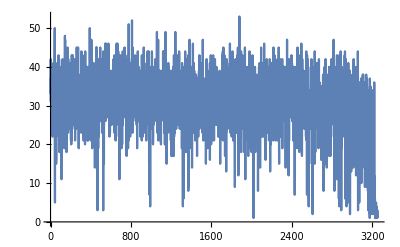
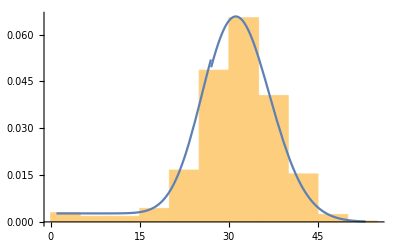
{-Graphics-,-Graphics-,<|μ→30.7598,√μ→5.54615,σ→7.35683,tot→100000,min→1,max→53|>}

```mathematica
countsStats[sampledCubieCounts[0.001^(1/2),2,100000]]
```

There are already, even in two dimensions, a noticeable number of deficiently populated cubies (the tail to the left of the peak above). These are the cubies in the corners outside the circle.

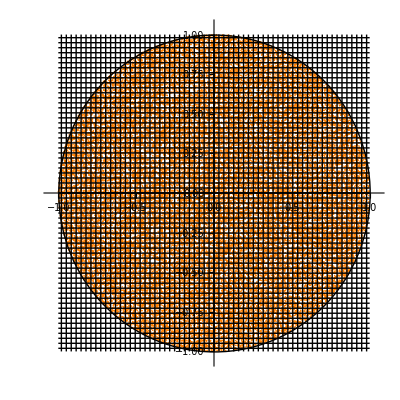

```mathematica
Show[show2D$[sampleDBall[2,40000]],Graphics[Circle[]],
Graphics@Line[{{#,-1},{#,1}}]&/@Range[0,1,0.001^(1/2)],
Graphics@Line[{{-1,#},{1,#}}]&/@Range[0,1,0.001^(1/2)],
Graphics@Line[{{#,-1},{#,1}}]&/@Range[0,-1,-0.001^(1/2)],
Graphics@Line[{{-1,#},{1,#}}]&/@Range[0,-1,-0.001^(1/2)]]
```

##### THREE DIMENSIONS

<|Number of Cubies = →1000.|>

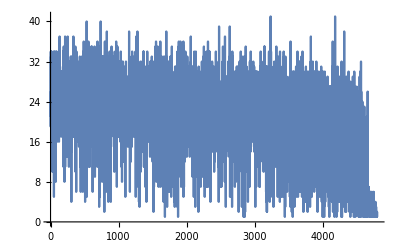
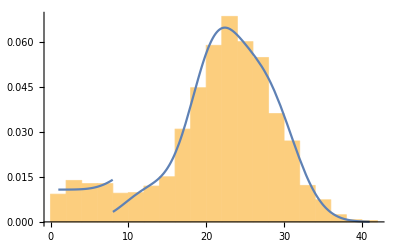
{-Graphics-,-Graphics-,<|μ→20.803,√μ→4.56103,σ→7.80517,tot→100000,min→1,max→41|>}

```mathematica
countsStats[sampledCubieCounts[0.001^(1/3),3,100000]]
```

In three dimensions, the number of deficient cubies is larger than “noticeable.”

##### SIX DIMENSIONS

<|Number of Cubies = →1000.|>

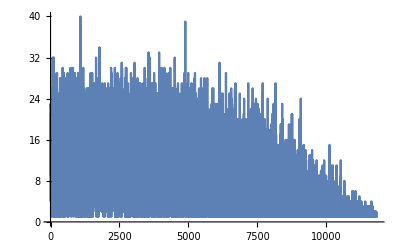
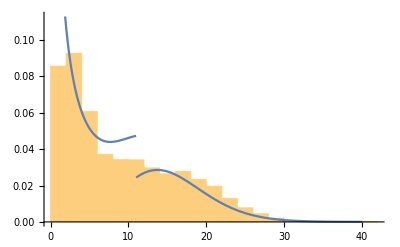
{-Graphics-,-Graphics-,<|μ→8.42815,√μ→2.90313,σ→7.12101,tot→100000,min→1,max→40|>}

```mathematica
countsStats[sampledCubieCounts[0.001^(1/6),6,100000]]
```

In six dimensions, the deficient cubies dominate the statistics.

##### TWENTY-SEVEN DIMENSIONS

<|Number of Cubies = →1000.|>

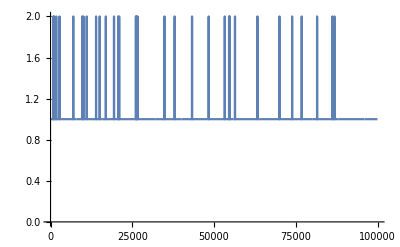
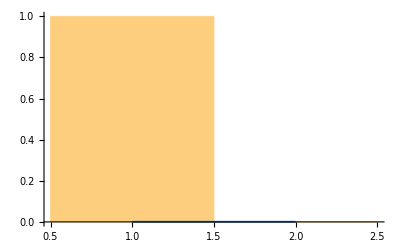
{-Graphics-,-Graphics-,<|μ→1.00032,√μ→1.00016,σ→0.0178886,tot→100000,min→1,max→2|>}

```mathematica
countsStats[sampledCubieCounts[0.001^(1/27),27,100000]]
```

In twenty-seven dimensions, virtually all the cubies are deficient.

There is no point in examining larger dimensions. To find cubies with non-zero populations (statistically), we must reduce the sizes of cubies, and thus increase their number and the computation time exponentially with dimension. It is not worth the computation time. We already have the shell method for verifying uniformity.

### STATISTICAL CONSTRUCTION

Alternatively to the geometrical constructions, sample uniformly on the (d+2)-sphere (not in the (d+2)-ball), then delete any two coordinates of each point, deterministically or at random. We already know how to sample uniformly on the (d+2)-sphere: normalized multinormals. The following code illustrates generating uniforms in the 1-ball from uniforms on the 3-sphere by dropping two, randomly chosen coordinates:

```mathematica
ClearAll[sampleDBall2];
sampleDBall2[d_,n_,e_:2]:=
RandomSample[#,e]&/@(* random rejection *)
Normalize/@ (* uniform on the d-sphere *)
RandomVariate[
MultinormalDistribution[IdentityMatrix[d+e]],n];
```

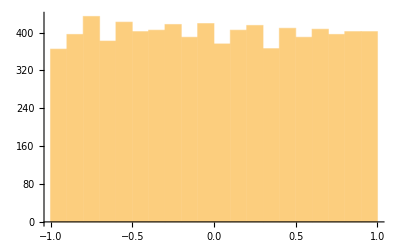

```mathematica
Histogram[Flatten[sampleDBall2[1,4000,2]]]
```

Why does this work? Why reject two coordinates at random, instead of one or three or seventeen?

First, realize that dropping one coordinate at random is the same as dropping the same coordinate from every point, at least for calculating the distribution of points, because all coordinates are sampled from the same distribution. Henceforth, we always drop the last two coordinates, z and y.

(THEOREM) The d-volume density of points is constant after projecting out z and y from a distribution constant per unit (d+2)-hyperspherical area.

We prove the theorem first for three dimensions, then argue extension to dimensions greater than three.

Plan: calculate the 2D point density after dropping z. Next, drop the y coordinate and prove the density of points on the x axis is independent of x.

As before, generate spherically uniform 3-vectors by sampling the 3-dimensional multinormal distribution, then normalizing the vectors:

```mathematica
show3D$[threeDPoints$=
Normalize/@
RandomVariate[
MultinormalDistribution[IdentityMatrix[3]],
40000]]
```

-Graphics3D-

Drop the z (last) coordinate of each point to produce a radially symmetric but non-uniform distribution in the 2-ball:

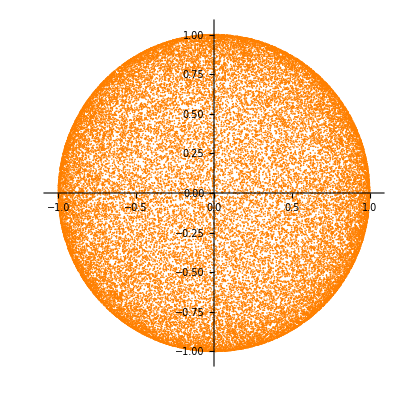

```mathematica
show2D$[(twoDPoints$=Drop[#,-1]&/@threeDPoints$)]
```

What is the 2D distribution at this step? (LEMMA) The 2D density of points is proportional to 1/√(1-r^2), where r<1 is the 2D distance from the origin. The density is unity near the origin and approaches infinity as r⟶1.

Proof of LEMMA:

Consider belts of equal z-height h on the 3-sphere surrounding the z axis. Each such belt has equal surface area 2π h on the 3-sphere. (Exercise: prove that belts of equal, finite or infinitesimal, z-height h around the surface of the 3-sphere of radius R have equal surface area 2π h R. In our case, R=1, so our belts have area 2π h). The following illustrates the belts in 3D:

```mathematica
Graphics3D[With[{dh=0.005,n=5,o={0,0,0}},
{Opacity[0.25],Sphere[],
Cone[{{0,0,#+dh},o},√(1-#^2)]&/@Range[0,1,1./n],
Cylinder[{o,{0,0,#+dh}},√(1-#^2)]&/@Range[0,1,1./n]}]]
```

-Graphics3D-

The following shows a longitudinal cross-section of the 3-ball with belts of equal z-height. The expression √(1-#^2) is a function-fragment that computes the 2D radius on the plane corresponding to a z-height n h, where n varies from 1 to some maximum integer N.

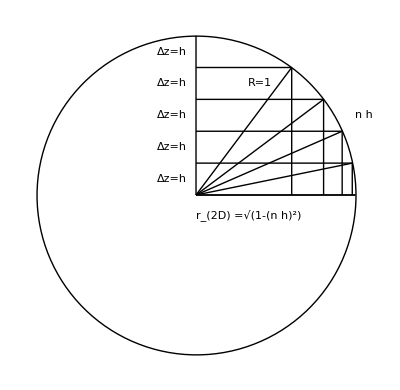

```mathematica
With[{o={0,0},N=5},
Graphics[{Circle[],
Text[Δz=h,{-0.15,#+0.5/N}]&/@Range[0,.99,1./N],
Text[n h,{1.05,0.5}],
Text[Subscript[r, 2D] =√(1-(n h)^2),{0.33,-.125}],
Text[R=1,{0.4,0.70}],
Line[{{0,#},{√(1-#^2),#}}&/@Range[0,.99,1./N]],
Line[{{√(1-#^2),0},{√(1-#^2),#}}&/@Range[0,.99,1./N]],
Line[{o,{√(1-#^2),#}}]&/@Range[0,1,1./N]}]]
```

The projected belts form annuli, or rings, in 2D. Consider the following projection of belts of z-height h=0.1 onto the 2D plane, along with the sample points, with their z coordinates dropped:

```mathematica
ClearAll[annuli];
annuli=Graphics@Circle[{0,0},√(1-#^2)]&/@Range[0,1,0.1];
Show[{show2D$[twoDPoints$]}~Join~annuli]
```

-Graphics-

The following illustrates a grouping function that isolates points in each annulus and shows a selection of one such group, the one with maximum z-height 0.8:

```mathematica
ClearAll[twoDPointsGroupedInAnnuli];
twoDPointsGroupedInAnnuli=GroupBy[twoDPoints$,Ceiling[√(1-Norm[#]^2),0.1]&];
Show[{show2D$[twoDPointsGroupedInAnnuli[0.8]]}~Join~annuli]
```

-Graphics-

The following illustrates that all annuli have, statistically, the same numbers of points.

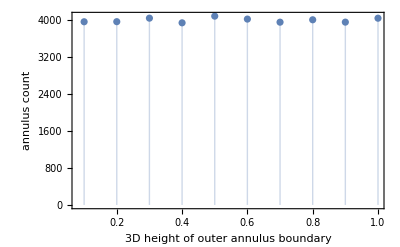

```mathematica
ListPlot[Length/@twoDPointsGroupedInAnnuli,
Filling->Axis,
PlotRange->{All,{0,All}},
Frame->True,
FrameLabel->{
{"annulus count",""},
{"3D height of outer annulus boundary","Annulus Count as a Function Cell["z",ExpressionUUID->"7aba8c8e-68bd-48ae-be25-02e29bfdbf3b"]-height"}}]
```

The following illustrates the 2D widths and 2D areas of the annuli as a function of z-height:

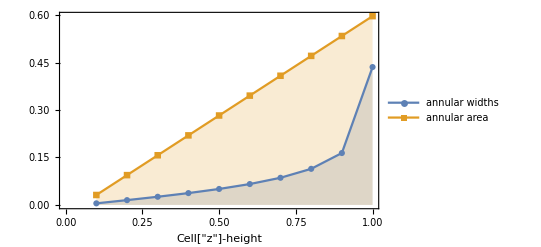

```mathematica
ListLinePlot[
With[{zs=Range[0,1,0.10]},
With[{rs=√(1-#^2)&/@zs},
{{Rest@zs,pairwise[#1-#2&,rs]}ᵀ,
{Rest@zs,pairwise[π(#1^2-#2^2)&,rs]}ᵀ}]],
Frame->True,PlotMarkers->Automatic,
FrameLabel->{{"",""},{"Cell["z",ExpressionUUID->"24788e15-f272-47aa-b6ab-08090297566e"]-height","Annular width and area versus Cell["z",ExpressionUUID->"e5418a73-8752-4334-9693-fb710b0b183d"]-height"}},
Filling->Axis,
PlotLegends->{"annular\nwidths","annular\narea"}]
```

Annular area is linear with z-height, and z-height varies as √(1-r^2). Point count per annular area is constant with z-height, so 2D point density against 2D r varies as 1/√(1-r^2).

Slice the circle vertically into bands of equal width Δx and y-height √(1-x^2):

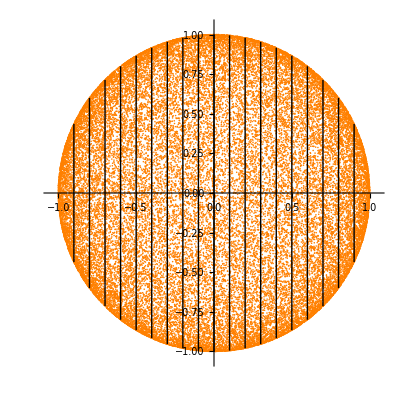

```mathematica
Show[{show2D$[twoDPoints$]}~Join~
(With[{y=√(1-#^2)},
Graphics@Line[{{#,-y},{#,y}}]]&/@Range[-1,1,0.1])]
```

Now integrate the density over the vertical band:

```mathematica
∫_(-√(1-x^2))^(√(1-x^2)) 1/(√(1-y^2-x^2))ⅆy
```

ConditionalExpression[π,-1≤Re[x]≤1&&Im[x]==0]

independent of x.

There follow statistics for sampling 1,000,000 points according to this scheme of rejecting two coordinates for two dimensions and 276 dimensions. As before, with a uniform distribution, we expect the standard deviations of counts to vary as the square root of the mean — the “eyeball” Chi-squared test for a uniform distribution.

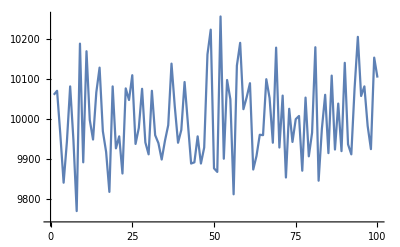
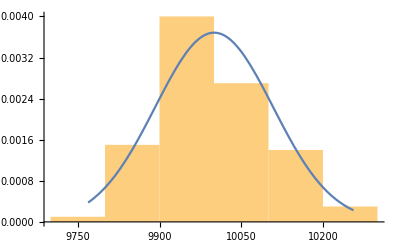
{-Graphics-,-Graphics-,<|μ→10000.,√μ→100.,σ→104.3,tot→1000000,min→9769,max→10256|>}

```mathematica
countsStats[sampledShellCounts2[0.01,2,1000000,sampleDBall2]]
```

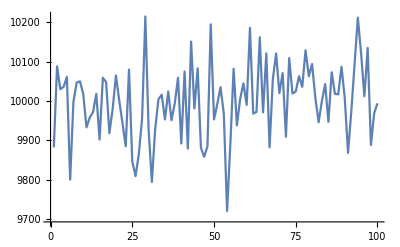
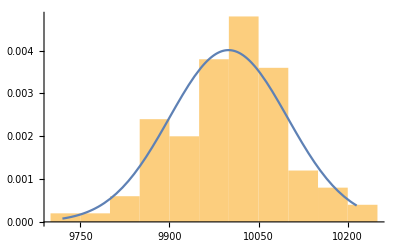
{-Graphics-,-Graphics-,<|μ→10000.,√μ→100.,σ→94.4868,tot→1000000,min→9720,max→10215|>}

```mathematica
countsStats[sampledShellCounts2[0.01,276,1000000]]
```

To extend the theorem to more dimensions, let x^2 stand for the Euclidean norm of all dimensions other than the last two. The integral still does not depend on x. ■